# Analysis of Insurance Companies’ reaction

Insurance companies are participating in more and more portfolio risk because their traditional portfolio which was composed of at least 50% low risk bonds is no longer profitable

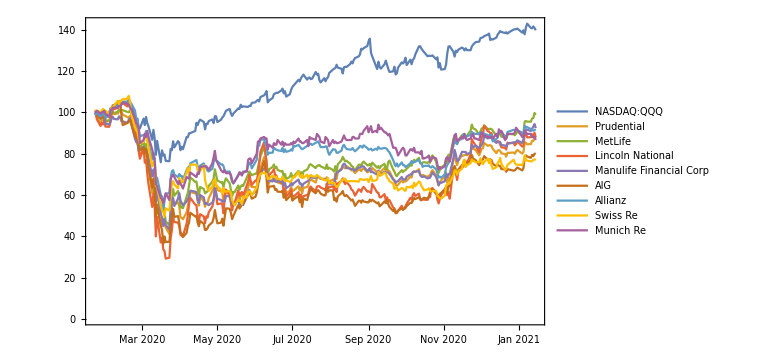

```mathematica
from := CurrentDate[]-Quantity[1, "Years"];
to := CurrentDate[];
period = "Day";

FetchStocks[labelToSymbol_, from_, to_, period_]:=Map[
FinancialData[
#,"CumulativeFractionalChange",{from, to, period}]&,
labelToSymbol
]

stocks = FetchStocks[
<|
"NASDAQ:QQQ"-> "NASDAQ:QQQ",
"Prudential"-> "NYSE:PRU",
"MetLife"-> "NYSE:MET",
"Lincoln National"-> "NYSE:LNC",
"Manulife Financial Corp"-> "NYSE:MFC",
"AIG"-> "NYSE:AIG",
"Allianz"-> "F:ALV",
"Swiss Re"-> "F:SR9A",
"Munich Re"-> "F:MUVB"
|>,
from, to,period
];

DateListPlot[Values[stocks],PlotLegends->Keys[stocks], ImageSize->Large]
```

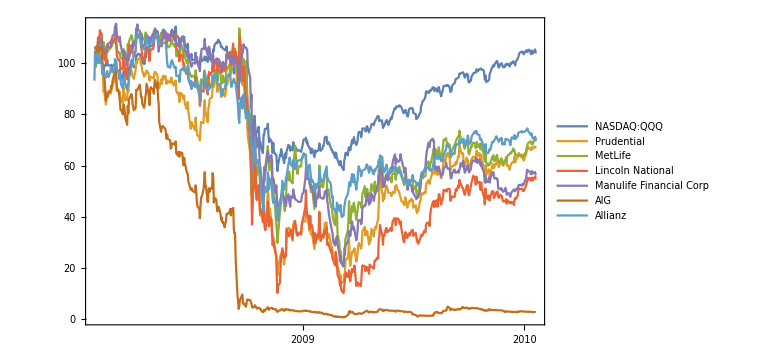

```mathematica
stocks = FetchStocks[
<|
"NASDAQ:QQQ"-> "NASDAQ:QQQ",
"Prudential"-> "NYSE:PRU",
"MetLife"-> "NYSE:MET",
"Lincoln National"-> "NYSE:LNC",
"Manulife Financial Corp"-> "NYSE:MFC",
"AIG"-> "NYSE:AIG",
"Allianz"-> "F:ALV"
|>,
CurrentDate[]-Quantity[13, "Years"], CurrentDate[]-Quantity[11, "Years"],period
];

DateListPlot[Values[stocks],PlotLegends->Keys[stocks], ImageSize->Large]
```

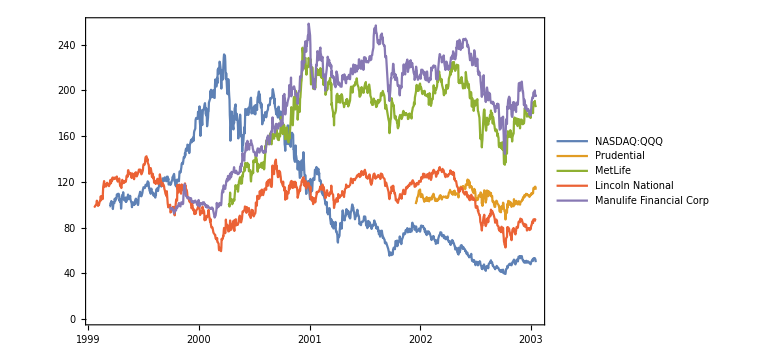

```mathematica
stocks = FetchStocks[
<|
"NASDAQ:QQQ"-> "NASDAQ:QQQ",
"Prudential"-> "NYSE:PRU",
"MetLife"-> "NYSE:MET",
"Lincoln National"-> "NYSE:LNC",
"Manulife Financial Corp"-> "NYSE:MFC"
|>,
CurrentDate[]-Quantity[22, "Years"], CurrentDate[]-Quantity[18, "Years"],period
];

DateListPlot[Values[stocks],PlotLegends->Keys[stocks], ImageSize->Large]
```